## Cuantico

## Definiciones de operadores

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
ClearAll;
Clear[Sz,SM,Sm,a2,Qp,QQ,PP,Sx,Sy,Szpp,SMSmpp,SmSMpp,SM2pp,Sm2pp,Sx2pp,F,P,Fpp,Ppp,Ut];

(*Operadores*)
Sz[J_]:=Sz[J]=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Qp[J_]:=Qp[J]=DiagonalMatrix[Table[Sqrt[i/2],{i,IntegerPart[2J]}],-1];
QQ[J_]:=QQ[J]=Qp[J]+Transpose[Qp[J]];
PP[J_]:=PP[J]=-I(Qp[J]-Transpose[Qp[J]]);
Sx[J_]:=Sx[J]=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);

(*Estados coherentes*)
Clear[a2,a2p];
(*a2[J_,Q_,P_]:=a2[J,Q,P]=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)],vec,alfa2},
vec=Table[If[alfa1==0&&i==-J,1,N[Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]]],{i,-J,J}];
Normalize[vec]
];*)

a2[J_,Q_,P_]:=Module[{z=-1+(Q^2+P^2)/2,ϕ=ArcTan[-(P/Q)]},
N[Table[1/((1+Tan[ArcCos[-z]/2]^2)^J)Sqrt[Binomial[2J,J+(m-J)]] Tan[ArcCos[-z]/2]^(J+(m-J))Exp[-I(J+(m-J))ϕ],{m,0,2J}],20]
];



Clear[F];
F[J_,α_,k_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α)(Sz[J])]];
```

## Survival probability

```mathematica
Clear[sur];
sur[ini_,n_]:=Module[{a},
Abs[(neweigenval^n).Abs[ini]^2]^2
];
```

```mathematica
Clear[J,α,k];
α=N[0.84];
k=30.0;
J=1000;
Qs={{2/10,7/10},{4832/10000,1},{71/100,106/100},{87/100,106/100},{55/100,172/100},{1165/1000,1602/1000}};
list=Table[i,{i,0,10000,1}];
```

```mathematica
mat=F[N[J],α,k];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
```

```mathematica
inicial=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,Qs}];
basefloq=ParallelTable[Conjugate[neweigenvec].i,{i,inicial}];
ipr=Table[Total[Abs[i]^4],{i,basefloq}];
```

```mathematica
ipr
```

{0.00102701,0.00102637,0.000983024,0.000977745,0.00101006,0.000965442}

```mathematica
Q=6;
Clear[data,data2];
data=ParallelTable[sur[basefloq[[Q]],i],{i,list}];
```

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{1,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
```

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{1,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
```

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{1,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
```

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{1,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
```

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{1,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
```

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{1,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
```

## Ejemplos

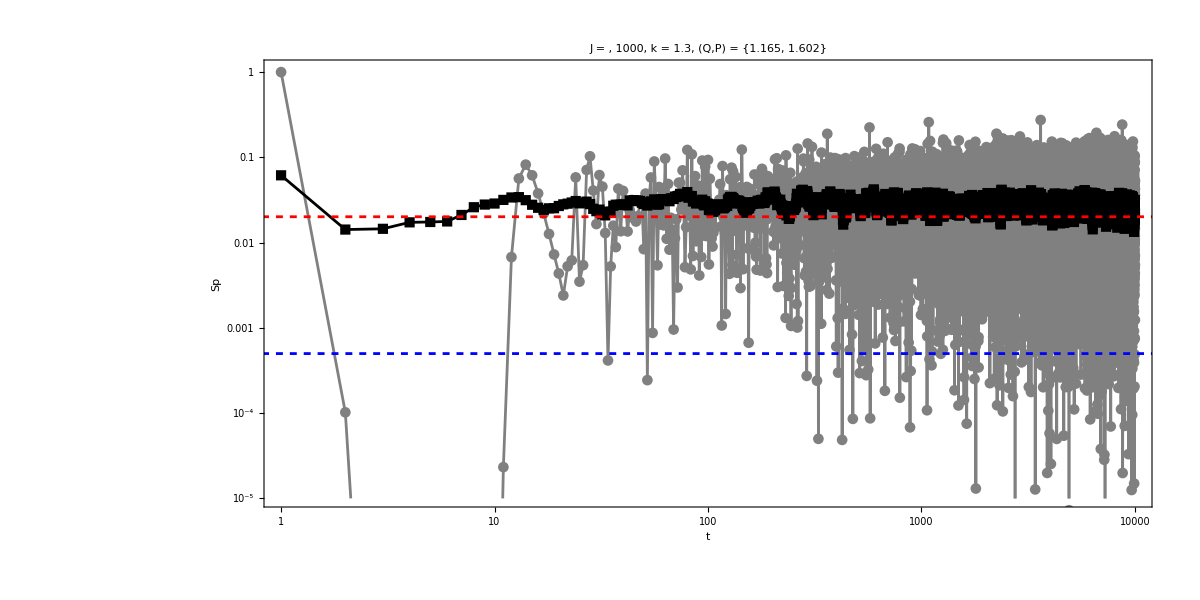

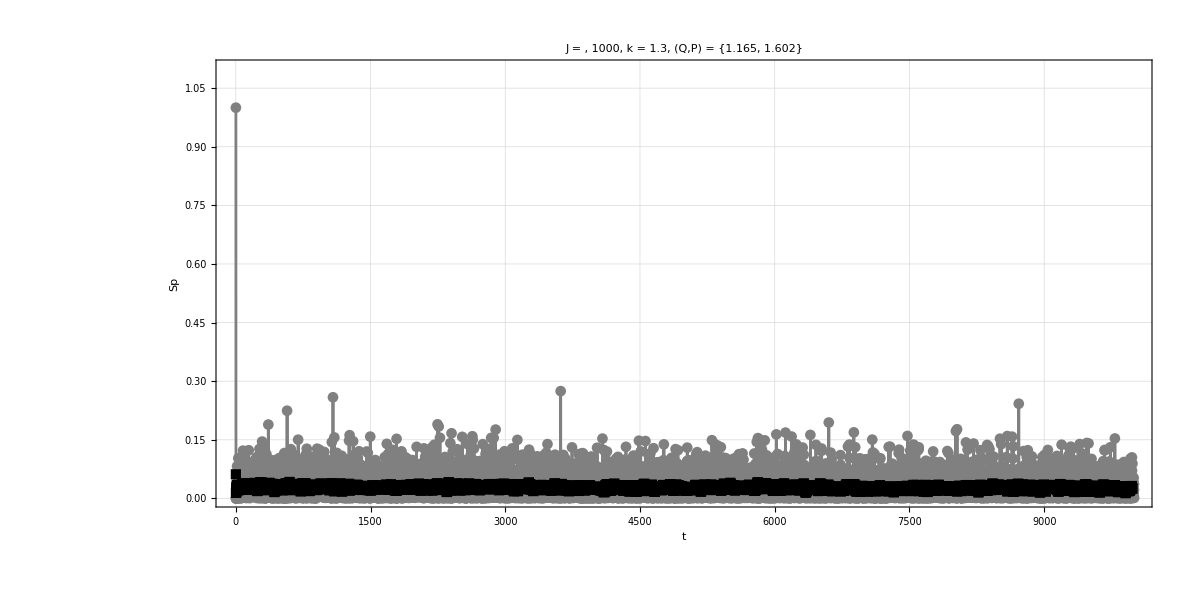

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{1,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
plot3=ListPlot[{data,data2},PlotRange->{{-20,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200]
```

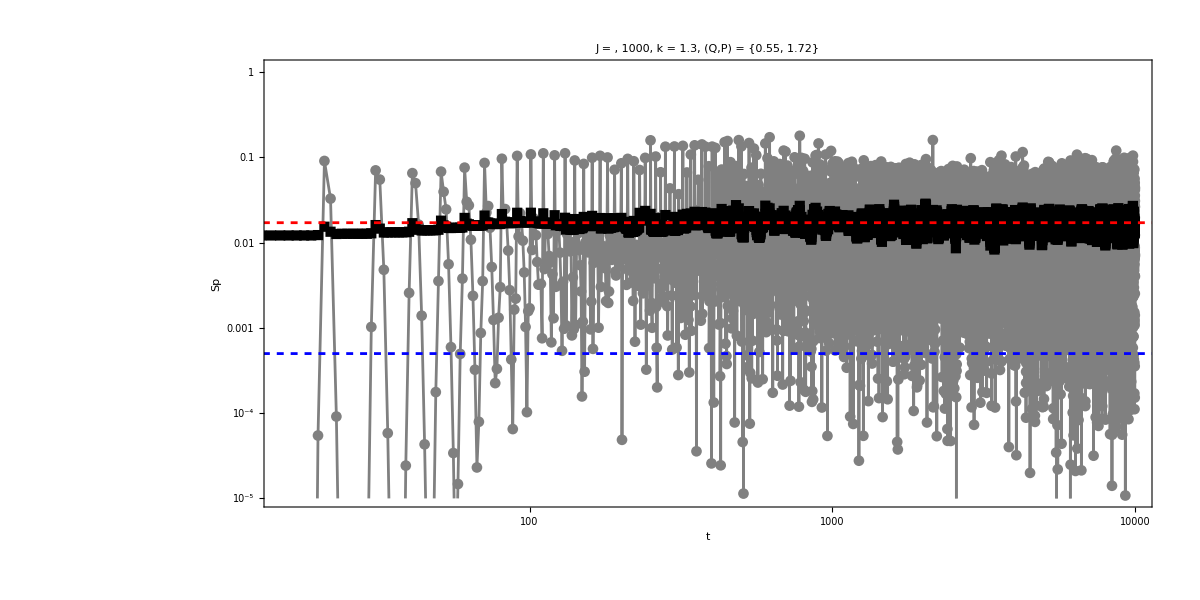

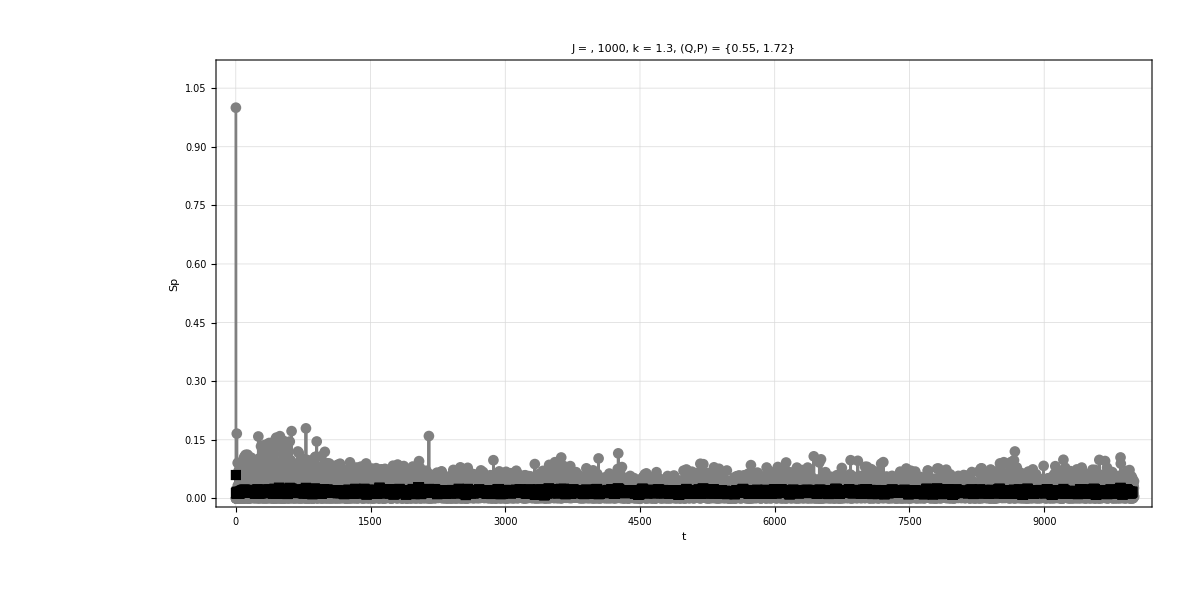

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{0,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
plot3=ListPlot[{data,data2},PlotRange->{{-20,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200]
```

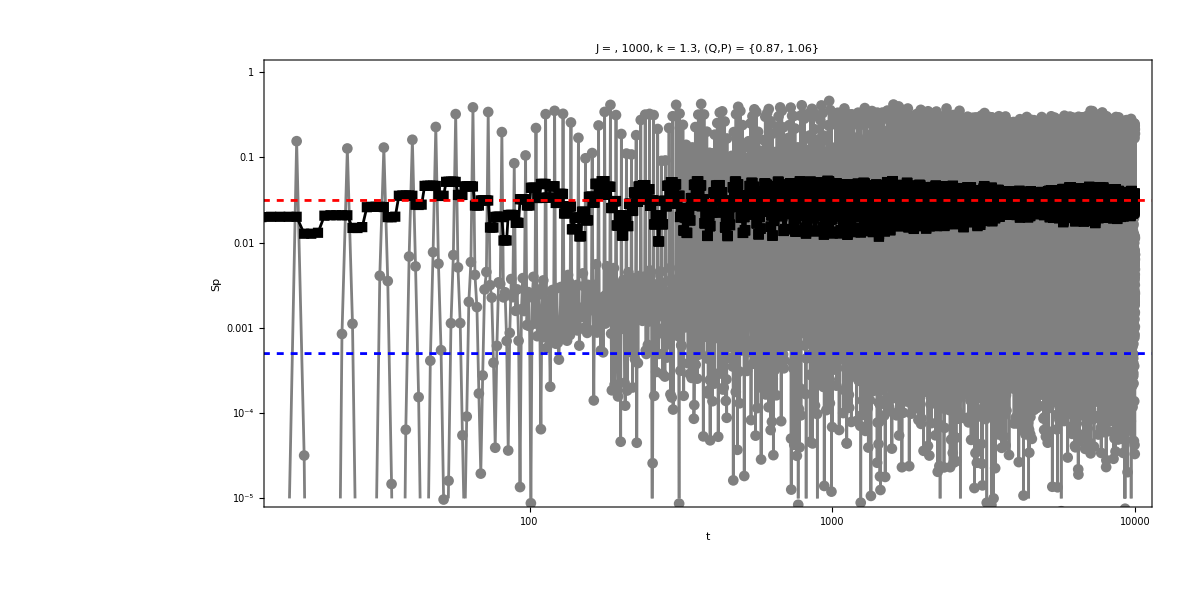

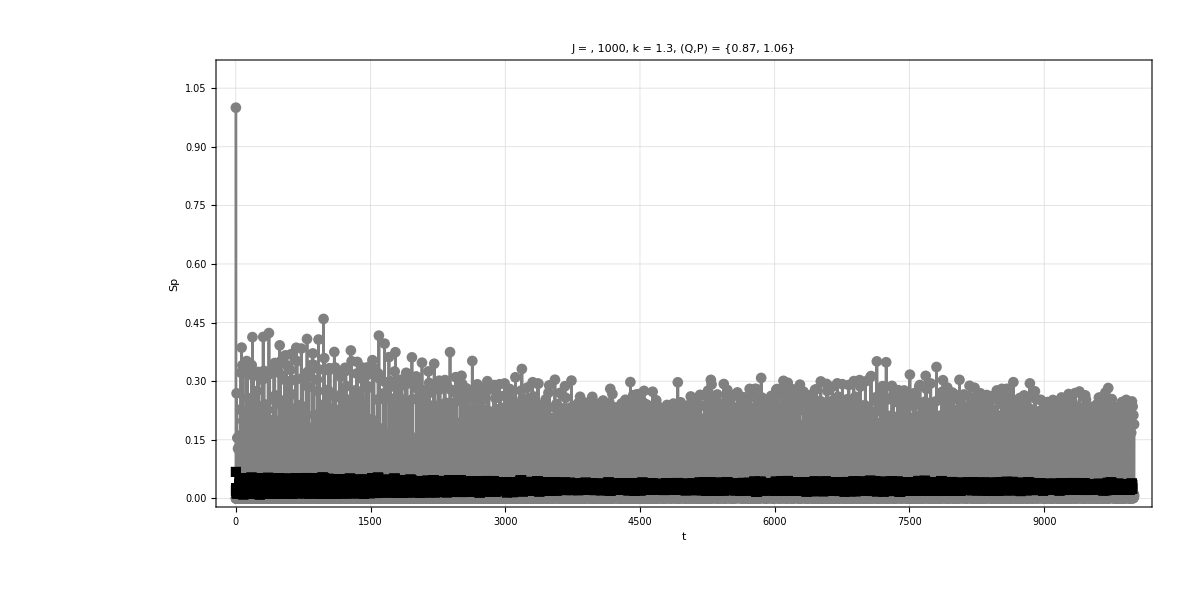

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{0,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
plot3=ListPlot[{data,data2},PlotRange->{{-20,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200]
```

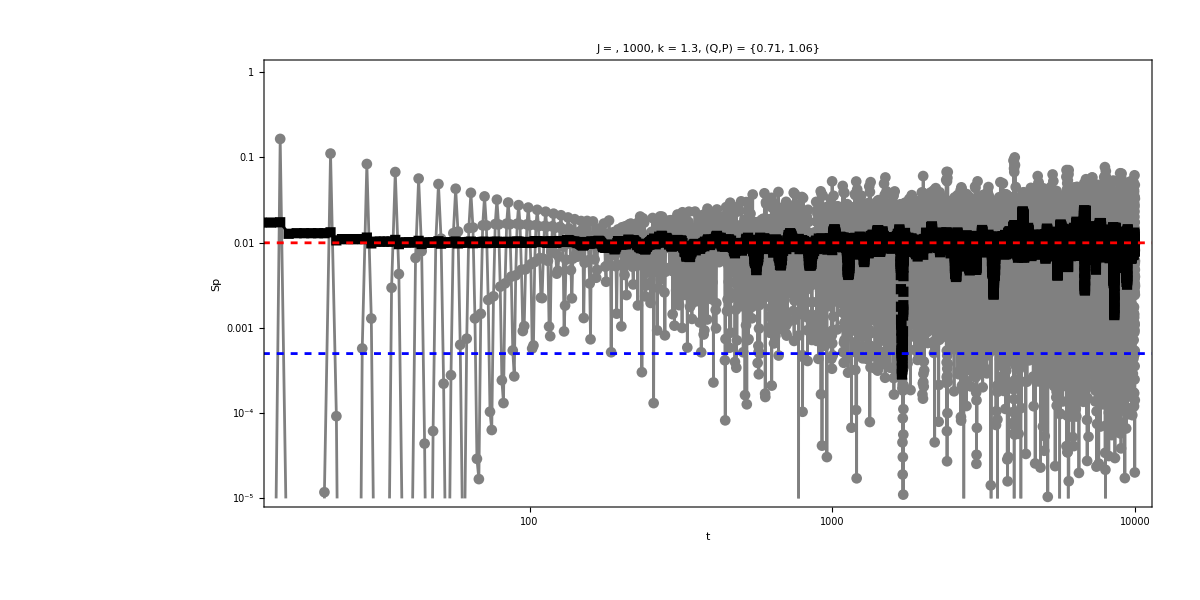

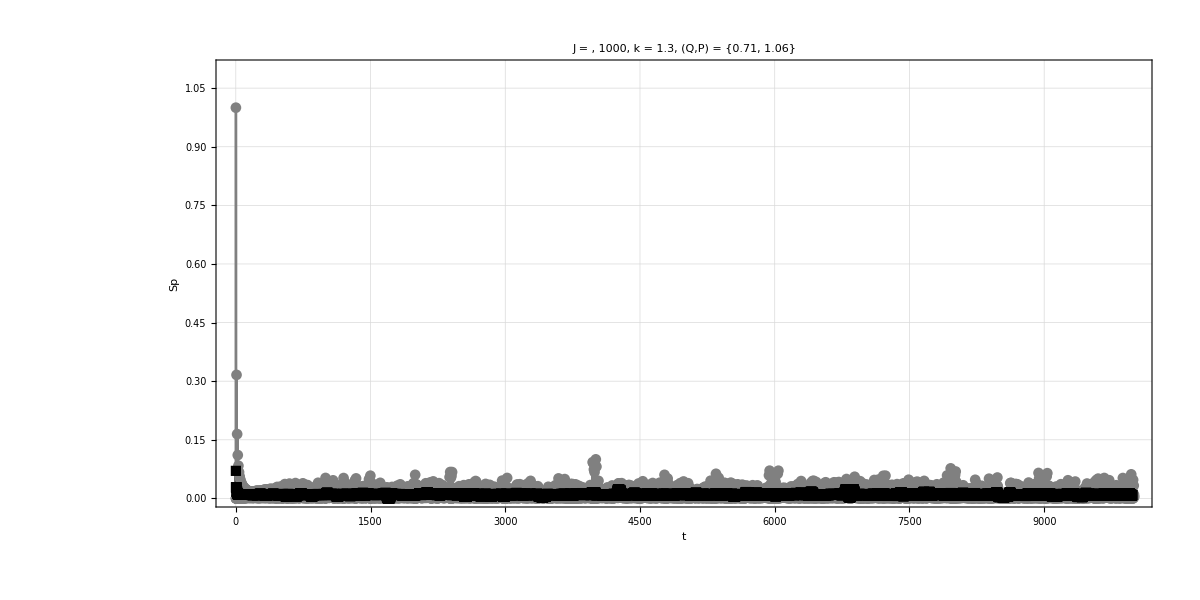

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{0,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
plot3=ListPlot[{data,data2},PlotRange->{{-20,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200]
```

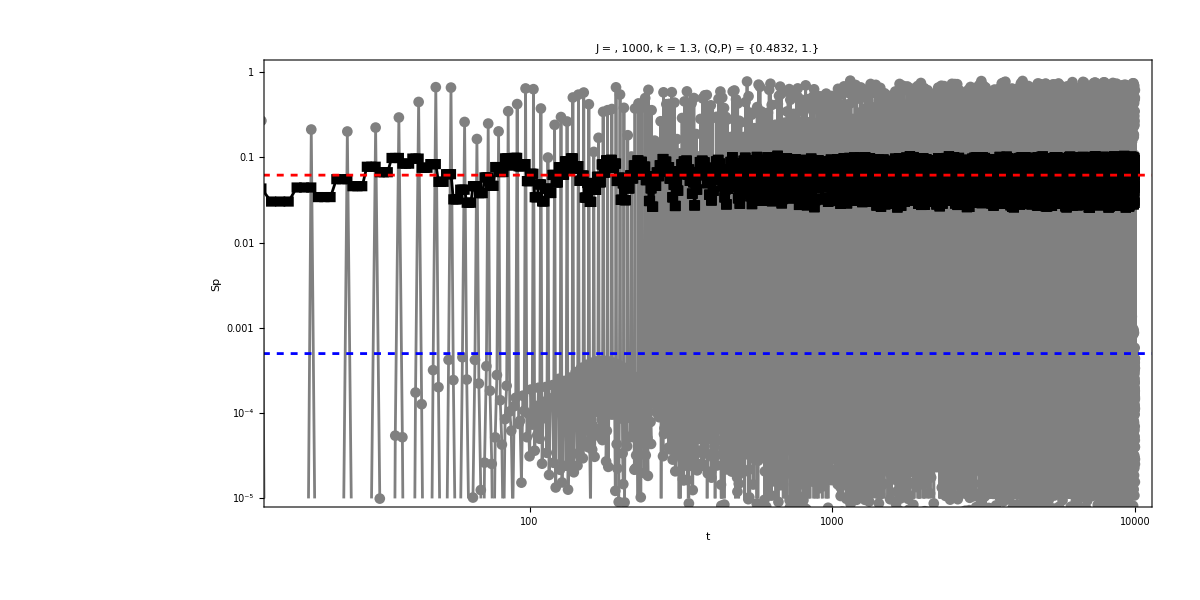

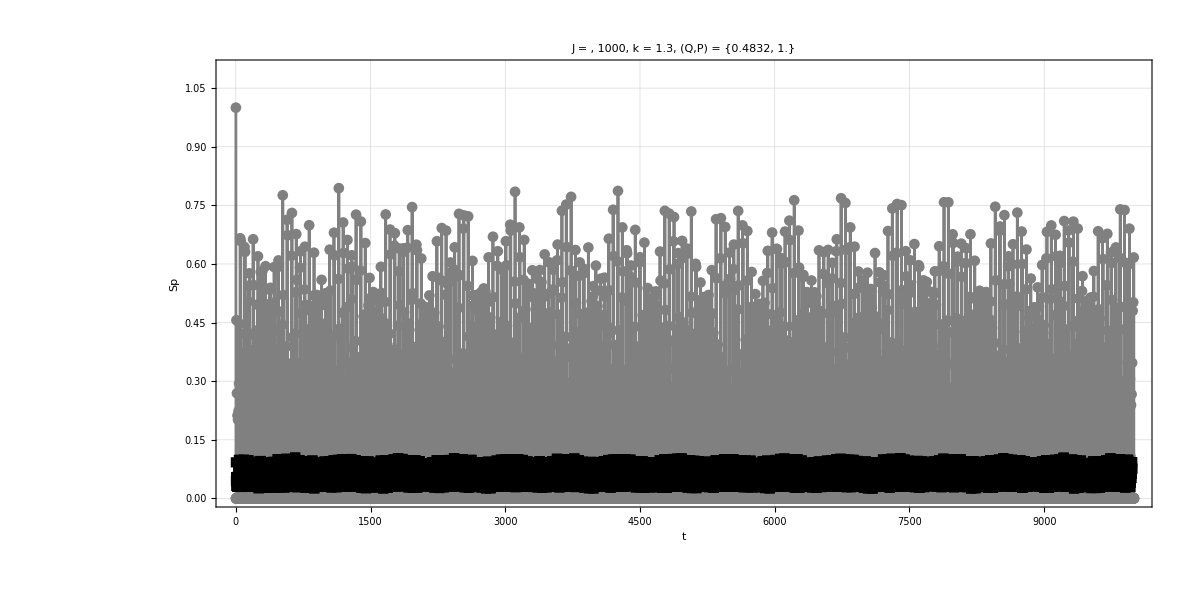

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{0,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
plot3=ListPlot[{data,data2},PlotRange->{{-20,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200]
```

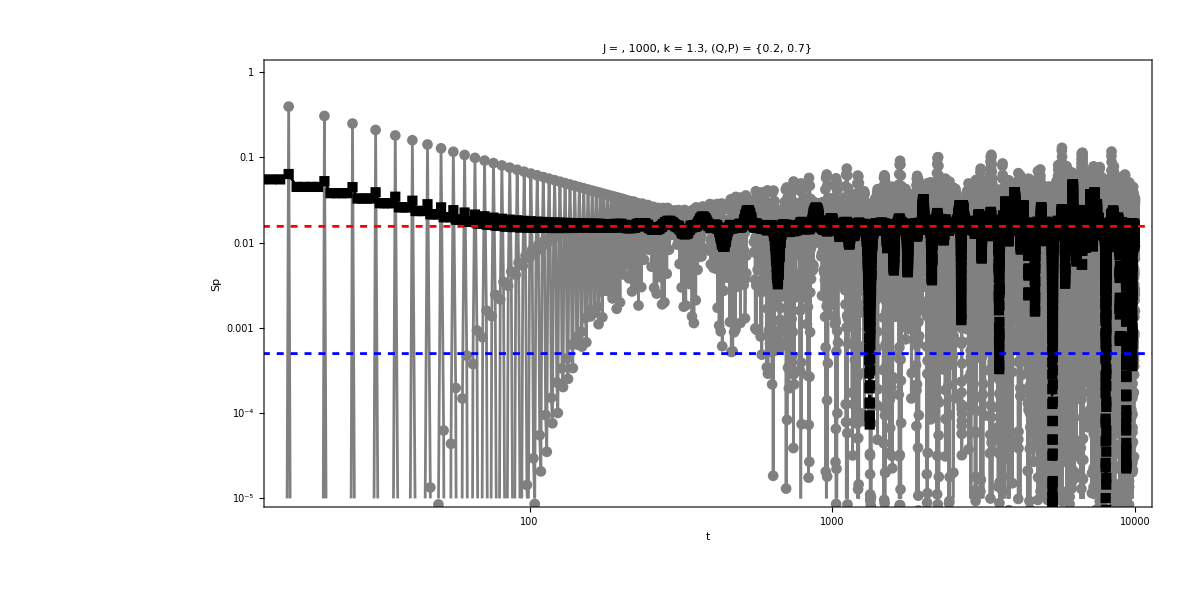

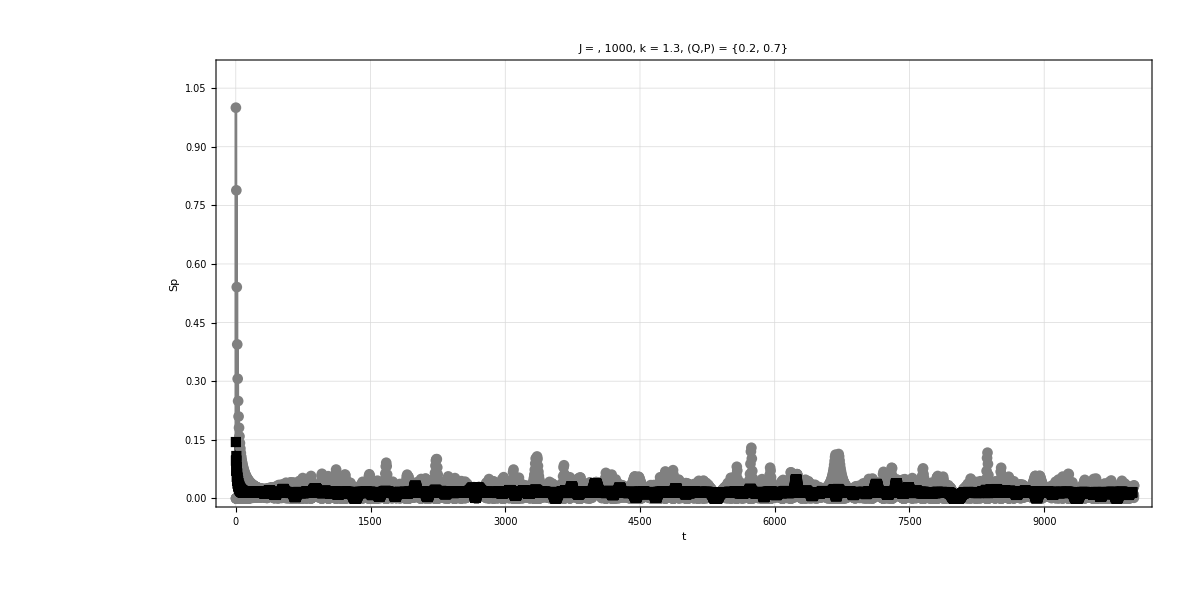

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr[[Q]],1/(2J+1)},{x,0.1,10^5},PlotStyle->{{Dashed,Red},{Dashed,Blue}}];
plot=ListLogLogPlot[{data,data2},PlotRange->{{0,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200];
survival100=Show[{plot,plot2},AspectRatio->1/2,ImageSize->1200]
plot3=ListPlot[{data,data2},PlotRange->{{-20,list[[-1]]},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->Automatic,Joined->True,PlotStyle->{Gray,Black},PlotLabel->Row[{Style["J = , ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[Qs[[Q]]]]<>"",24,Black]}],FrameLabel->{"t","Sp"},LabelStyle->Directive[ 18,Black],AspectRatio->1/2,ImageSize->1200]
```